## Time-dependent TFD State on a Periodic Lattice

```mathematica
Quit[];
```

```mathematica
ClearAll["Global`*"]
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

First step: Import the GaussianOptimization Package (Run):

```mathematica
Import["/Users/HugoCamargo89/Desktop/gaussian_purifications/Mathematica Code/GaussianOptimization.m"]
```

```mathematica
(*<<GaussianOptimization`*)
```

In this Chapter of the Mathematica notebook, we use the optimization procedure to find the complexity of purification CoP for time-independent Thermal states and time-dependent TFD states on a circle. The SubChapter: Definitions (Run), should be run at the beginning, as it has the necessary field-theoretic definitions for the physical system in question.

Definitions (Run)

The following definitions are the revised field-theoretic definitions for the covariance matrix. The parameters of the theory are the following:

1. Total number of lattice sites: NN,
2. Inverse Temperature: β,
3. Time t,
4. Mass of the Scalar Field: m,
5. Lattice Spacing: δ,
6. Dimension of subsystems on the lattice: dimA1 & dimB1,
7. Lattice Site Separation between the subsystems: d,
8. Dimension of purifications: dimPur
9. Total length of the circle: L=NNδ . (! Counting starts at site 0 !)
10. Length of the subsystem: l=(dimA1+dimB1)δ
11. Ratio of subsystem/sistem size: l/L=(dimA1+dimB1)/NN (! Counting starts at site 0 !)

```mathematica
ω[NN_,δ_,m_,k_]:=ω[NN,δ,m,k]=√(m^2+(2/δ Sin[(π k)/NN])^2);
```

```mathematica
α[NN_,δ_,m_,k_,β_]:=α[NN,δ,m,k,β]=1/2 Log[Coth[(β ω[NN,δ,m,k])/4]];
```

### Thermal States (Time-independent)

The relevant quantities that are calculated from these parameters are the full covariance matrices of the thermal state (assuming a small mass m) KGThft[{NN,δ,m,β}], as well as the partial covariance matrix for the subsystem consisting of two sets of lattice sites. These can be set to be adjacent or disjoint, depending on the parameter d (lattice site separation between the subsystems) KGThcmRes[{NN,δ,m,β},{dimA,dimB,d}].

Notice that input for KGThft is a list: {NN,δ,m,β}:

```mathematica
KGThft[{NN_,δ_,m_,β_}]:=KGThft[{NN,δ,m,β}]={Fourier[Table[1/(√NN)(Cosh[2α[NN,δ,m,k,β]]ω[NN,δ,m,k]),{k,0,NN-1}]]//Re,Fourier[Table[1/(√NN)(Cosh[2α[NN,δ,m,k,β]]/ω[NN,δ,m,k]),{k,0,NN-1}]]//Re};(*First entry are π correlators, second one are ϕ correlators.*)
KGThb[var_]:=KGThb[var]={ToeplitzMatrix[KGThft[var]⟦1⟧],ToeplitzMatrix[KGThft[var]⟦2⟧]};
KGThcm[var_]:=KGThcm[var]=ArrayFlatten[ReleaseHold[DiagonalMatrix[Hold/@{KGThb[var]⟦1⟧,KGThb[var]⟦2⟧}]]];(* Thermal State Full System Covariance Matrix in qqpp basis *)
```

```mathematica
KGThcmqpqp[{NN_,δ_,m_,β_}]:=KGThcmqpqp[{NN,δ,m,β}]=GOqpqpFROMqqpp[NN].KGThcm[{NN,δ,m,β}].Transpose[GOqpqpFROMqqpp[NN]];(* Thermal State Full System Covariance Matrix in qpqp basis *)
```

```mathematica
KGThcmRes[var_,{dimA_,dimB_,d_}]:=KGThcmRes[var,{dimA,dimB,d}]=Module[{ind},
ind=Join[Table[i,{i,dimA}],Table[i+dimA+d,{i,dimB}]];
GOqpqpFROMqqpp[dimA+dimB].ArrayFlatten[ArrayFlatten[ReleaseHold[DiagonalMatrix[Hold/@{KGThb[var]⟦1,ind,ind⟧,KGThb[var]⟦2,ind,ind⟧}]]].Transpose[GOqpqpFROMqqpp[dimA+dimB]]
]](*  Thermal State Subsystem Covariance Matrixin qpqp basis *)
```

#### TFD States (time-dependent)

```mathematica
MTFDft[{t_,NN_,δ_,m_,β_}]:=MTFDft[{t,NN,δ,m,β}]=1/(√NN){Fourier[Table[(Cosh[2α[NN,δ,m,k,β]]/ω[NN,δ,m,k]),{k,0,NN-1}]]//Re,Fourier[Table[(Cosh[2α[NN,δ,m,k,β]]ω[NN,δ,m,k]),{k,0,NN-1}]]//Re,Fourier[Table[-(Cos[t ω[NN,δ,m,k]]Sinh[2α[NN,δ,m,k,β]])/ω[NN,δ,m,k] ,{k,0,NN-1}]]//Re,Fourier[Table[(ω[NN,δ,m,k]Cos[t ω[NN,δ,m,k]]Sinh[2α[NN,δ,m,k,β]]),{k,0,NN-1}]]//Re,Fourier[Table[(Sinh[2α[NN,δ,m,k,β]]Sin[t ω[NN,δ,m,k]]),{k,0,NN-1}]]//Re};
```

```mathematica
MTFDb[var_]:=MTFDb[var]={ToeplitzMatrix[MTFDft[var]⟦1⟧],ToeplitzMatrix[MTFDft[var]⟦2⟧],ToeplitzMatrix[MTFDft[var]⟦3⟧],ToeplitzMatrix[MTFDft[var]⟦4⟧],ToeplitzMatrix[MTFDft[var]⟦5⟧]};
MTFDcm[var_]:=MTFDcm[var]=ArrayFlatten[({{MTFDb[var]⟦1⟧, 0, MTFDb[var]⟦3⟧, MTFDb[var]⟦5⟧}, {0, MTFDb[var]⟦2⟧, MTFDb[var]⟦5⟧, MTFDb[var]⟦4⟧}, {MTFDb[var]⟦3⟧, MTFDb[var]⟦5⟧, MTFDb[var]⟦1⟧, 0}, {MTFDb[var]⟦5⟧, MTFDb[var]⟦4⟧, 0, MTFDb[var]⟦2⟧}})];(* in qqpp basis *)
```

```mathematica
MTFDcm[{0,10,1,1/10,100000}]//MatrixForm
```

(1.76728 | 1.13782 | 0.944148 | 0.84646 | 0.797055 | 0.781758 | 0.797055 | 0.84646 | 0.944148 | 1.13782 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
1.13782 | 1.76728 | 1.13782 | 0.944148 | 0.84646 | 0.797055 | 0.781758 | 0.797055 | 0.84646 | 0.944148 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.944148 | 1.13782 | 1.76728 | 1.13782 | 0.944148 | 0.84646 | 0.797055 | 0.781758 | 0.797055 | 0.84646 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.84646 | 0.944148 | 1.13782 | 1.76728 | 1.13782 | 0.944148 | 0.84646 | 0.797055 | 0.781758 | 0.797055 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.797055 | 0.84646 | 0.944148 | 1.13782 | 1.76728 | 1.13782 | 0.944148 | 0.84646 | 0.797055 | 0.781758 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.781758 | 0.797055 | 0.84646 | 0.944148 | 1.13782 | 1.76728 | 1.13782 | 0.944148 | 0.84646 | 0.797055 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.797055 | 0.781758 | 0.797055 | 0.84646 | 0.944148 | 1.13782 | 1.76728 | 1.13782 | 0.944148 | 0.84646 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.84646 | 0.797055 | 0.781758 | 0.797055 | 0.84646 | 0.944148 | 1.13782 | 1.76728 | 1.13782 | 0.944148 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.944148 | 0.84646 | 0.797055 | 0.781758 | 0.797055 | 0.84646 | 0.944148 | 1.13782 | 1.76728 | 1.13782 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
1.13782 | 0.944148 | 0.84646 | 0.797055 | 0.781758 | 0.797055 | 0.84646 | 0.944148 | 1.13782 | 1.76728 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.2766 | -0.424417 | -0.0865386 | -0.0398191 | -0.0261367 | -0.0227773 | -0.0261367 | -0.0398191 | -0.0865386 | -0.424417 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.424417 | 1.2766 | -0.424417 | -0.0865386 | -0.0398191 | -0.0261367 | -0.0227773 | -0.0261367 | -0.0398191 | -0.0865386 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.0865386 | -0.424417 | 1.2766 | -0.424417 | -0.0865386 | -0.0398191 | -0.0261367 | -0.0227773 | -0.0261367 | -0.0398191 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.0398191 | -0.0865386 | -0.424417 | 1.2766 | -0.424417 | -0.0865386 | -0.0398191 | -0.0261367 | -0.0227773 | -0.0261367 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.0261367 | -0.0398191 | -0.0865386 | -0.424417 | 1.2766 | -0.424417 | -0.0865386 | -0.0398191 | -0.0261367 | -0.0227773 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.0227773 | -0.0261367 | -0.0398191 | -0.0865386 | -0.424417 | 1.2766 | -0.424417 | -0.0865386 | -0.0398191 | -0.0261367 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.0261367 | -0.0227773 | -0.0261367 | -0.0398191 | -0.0865386 | -0.424417 | 1.2766 | -0.424417 | -0.0865386 | -0.0398191 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.0398191 | -0.0261367 | -0.0227773 | -0.0261367 | -0.0398191 | -0.0865386 | -0.424417 | 1.2766 | -0.424417 | -0.0865386 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.0865386 | -0.0398191 | -0.0261367 | -0.0227773 | -0.0261367 | -0.0398191 | -0.0865386 | -0.424417 | 1.2766 | -0.424417 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.424417 | -0.0865386 | -0.0398191 | -0.0261367 | -0.0227773 | -0.0261367 | -0.0398191 | -0.0865386 | -0.424417 | 1.2766 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1.76728 | 1.13782 | 0.944148 | 0.84646 | 0.797055 | 0.781758 | 0.797055 | 0.84646 | 0.944148 | 1.13782 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1.13782 | 1.76728 | 1.13782 | 0.944148 | 0.84646 | 0.797055 | 0.781758 | 0.797055 | 0.84646 | 0.944148 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.944148 | 1.13782 | 1.76728 | 1.13782 | 0.944148 | 0.84646 | 0.797055 | 0.781758 | 0.797055 | 0.84646 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.84646 | 0.944148 | 1.13782 | 1.76728 | 1.13782 | 0.944148 | 0.84646 | 0.797055 | 0.781758 | 0.797055 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.797055 | 0.84646 | 0.944148 | 1.13782 | 1.76728 | 1.13782 | 0.944148 | 0.84646 | 0.797055 | 0.781758 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.781758 | 0.797055 | 0.84646 | 0.944148 | 1.13782 | 1.76728 | 1.13782 | 0.944148 | 0.84646 | 0.797055 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.797055 | 0.781758 | 0.797055 | 0.84646 | 0.944148 | 1.13782 | 1.76728 | 1.13782 | 0.944148 | 0.84646 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.84646 | 0.797055 | 0.781758 | 0.797055 | 0.84646 | 0.944148 | 1.13782 | 1.76728 | 1.13782 | 0.944148 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.944148 | 0.84646 | 0.797055 | 0.781758 | 0.797055 | 0.84646 | 0.944148 | 1.13782 | 1.76728 | 1.13782 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1.13782 | 0.944148 | 0.84646 | 0.797055 | 0.781758 | 0.797055 | 0.84646 | 0.944148 | 1.13782 | 1.76728 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.2766 | -0.424417 | -0.0865386 | -0.0398191 | -0.0261367 | -0.0227773 | -0.0261367 | -0.0398191 | -0.0865386 | -0.424417
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.424417 | 1.2766 | -0.424417 | -0.0865386 | -0.0398191 | -0.0261367 | -0.0227773 | -0.0261367 | -0.0398191 | -0.0865386
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.0865386 | -0.424417 | 1.2766 | -0.424417 | -0.0865386 | -0.0398191 | -0.0261367 | -0.0227773 | -0.0261367 | -0.0398191
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.0398191 | -0.0865386 | -0.424417 | 1.2766 | -0.424417 | -0.0865386 | -0.0398191 | -0.0261367 | -0.0227773 | -0.0261367
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.0261367 | -0.0398191 | -0.0865386 | -0.424417 | 1.2766 | -0.424417 | -0.0865386 | -0.0398191 | -0.0261367 | -0.0227773
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.0227773 | -0.0261367 | -0.0398191 | -0.0865386 | -0.424417 | 1.2766 | -0.424417 | -0.0865386 | -0.0398191 | -0.0261367
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.0261367 | -0.0227773 | -0.0261367 | -0.0398191 | -0.0865386 | -0.424417 | 1.2766 | -0.424417 | -0.0865386 | -0.0398191
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.0398191 | -0.0261367 | -0.0227773 | -0.0261367 | -0.0398191 | -0.0865386 | -0.424417 | 1.2766 | -0.424417 | -0.0865386
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.0865386 | -0.0398191 | -0.0261367 | -0.0227773 | -0.0261367 | -0.0398191 | -0.0865386 | -0.424417 | 1.2766 | -0.424417
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.424417 | -0.0865386 | -0.0398191 | -0.0261367 | -0.0227773 | -0.0261367 | -0.0398191 | -0.0865386 | -0.424417 | 1.2766)

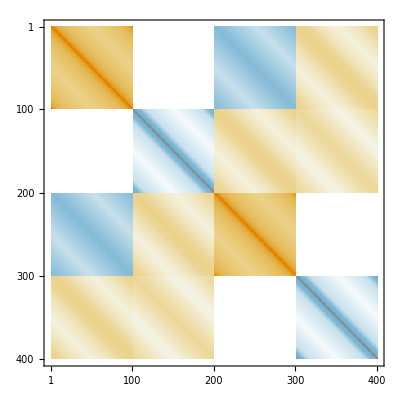

```mathematica
MatrixPlot[MTFDcm[{1.4,100,1,1/10,100}]]
```

```mathematica
MTFDqpqp[{t_,NN_,δ_,m_,β_}]:=Module[{Mqqpp,Mtra,MTra},
Mqqpp=MTFDcm[{t,NN,δ,m,β}];
Mtra=GOqpqpFROMqqpp[NN];
MTra=ArrayFlatten[ReleaseHold[DiagonalMatrix[Hold/@{Mtra,Mtra}]]];
MTra.Mqqpp.Transpose[MTra]
];
```

```mathematica
MTFDqpqp[{t,NN,δ,m,β}]//MatrixForm
```

(2.08435 | 0. | 1.46008 | 0. | 1.28274 | 0. | 1.215 | 0. | 1.215 | 0. | 1.28274 | 0. | 1.46008 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 1.26937 | 0. | -0.432315 | 0. | -0.096786 | 0. | -0.0555829 | 0. | -0.0555829 | 0. | -0.096786 | 0. | -0.432315 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
1.46008 | 0. | 2.08435 | 0. | 1.46008 | 0. | 1.28274 | 0. | 1.215 | 0. | 1.215 | 0. | 1.28274 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | -0.432315 | 0. | 1.26937 | 0. | -0.432315 | 0. | -0.096786 | 0. | -0.0555829 | 0. | -0.0555829 | 0. | -0.096786 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
1.28274 | 0. | 1.46008 | 0. | 2.08435 | 0. | 1.46008 | 0. | 1.28274 | 0. | 1.215 | 0. | 1.215 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | -0.096786 | 0. | -0.432315 | 0. | 1.26937 | 0. | -0.432315 | 0. | -0.096786 | 0. | -0.0555829 | 0. | -0.0555829 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
1.215 | 0. | 1.28274 | 0. | 1.46008 | 0. | 2.08435 | 0. | 1.46008 | 0. | 1.28274 | 0. | 1.215 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | -0.0555829 | 0. | -0.096786 | 0. | -0.432315 | 0. | 1.26937 | 0. | -0.432315 | 0. | -0.096786 | 0. | -0.0555829 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
1.215 | 0. | 1.215 | 0. | 1.28274 | 0. | 1.46008 | 0. | 2.08435 | 0. | 1.46008 | 0. | 1.28274 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | -0.0555829 | 0. | -0.0555829 | 0. | -0.096786 | 0. | -0.432315 | 0. | 1.26937 | 0. | -0.432315 | 0. | -0.096786 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
1.28274 | 0. | 1.215 | 0. | 1.215 | 0. | 1.28274 | 0. | 1.46008 | 0. | 2.08435 | 0. | 1.46008 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | -0.096786 | 0. | -0.0555829 | 0. | -0.0555829 | 0. | -0.096786 | 0. | -0.432315 | 0. | 1.26937 | 0. | -0.432315 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
1.46008 | 0. | 1.28274 | 0. | 1.215 | 0. | 1.215 | 0. | 1.28274 | 0. | 1.46008 | 0. | 2.08435 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | -0.432315 | 0. | -0.096786 | 0. | -0.0555829 | 0. | -0.0555829 | 0. | -0.096786 | 0. | -0.432315 | 0. | 1.26937 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 2.08435 | 0. | 1.46008 | 0. | 1.28274 | 0. | 1.215 | 0. | 1.215 | 0. | 1.28274 | 0. | 1.46008 | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1.26937 | 0. | -0.432315 | 0. | -0.096786 | 0. | -0.0555829 | 0. | -0.0555829 | 0. | -0.096786 | 0. | -0.432315
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1.46008 | 0. | 2.08435 | 0. | 1.46008 | 0. | 1.28274 | 0. | 1.215 | 0. | 1.215 | 0. | 1.28274 | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.432315 | 0. | 1.26937 | 0. | -0.432315 | 0. | -0.096786 | 0. | -0.0555829 | 0. | -0.0555829 | 0. | -0.096786
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1.28274 | 0. | 1.46008 | 0. | 2.08435 | 0. | 1.46008 | 0. | 1.28274 | 0. | 1.215 | 0. | 1.215 | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.096786 | 0. | -0.432315 | 0. | 1.26937 | 0. | -0.432315 | 0. | -0.096786 | 0. | -0.0555829 | 0. | -0.0555829
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1.215 | 0. | 1.28274 | 0. | 1.46008 | 0. | 2.08435 | 0. | 1.46008 | 0. | 1.28274 | 0. | 1.215 | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.0555829 | 0. | -0.096786 | 0. | -0.432315 | 0. | 1.26937 | 0. | -0.432315 | 0. | -0.096786 | 0. | -0.0555829
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1.215 | 0. | 1.215 | 0. | 1.28274 | 0. | 1.46008 | 0. | 2.08435 | 0. | 1.46008 | 0. | 1.28274 | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.0555829 | 0. | -0.0555829 | 0. | -0.096786 | 0. | -0.432315 | 0. | 1.26937 | 0. | -0.432315 | 0. | -0.096786
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1.28274 | 0. | 1.215 | 0. | 1.215 | 0. | 1.28274 | 0. | 1.46008 | 0. | 2.08435 | 0. | 1.46008 | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.096786 | 0. | -0.0555829 | 0. | -0.0555829 | 0. | -0.096786 | 0. | -0.432315 | 0. | 1.26937 | 0. | -0.432315
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1.46008 | 0. | 1.28274 | 0. | 1.215 | 0. | 1.215 | 0. | 1.28274 | 0. | 1.46008 | 0. | 2.08435 | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.432315 | 0. | -0.096786 | 0. | -0.0555829 | 0. | -0.0555829 | 0. | -0.096786 | 0. | -0.432315 | 0. | 1.26937)

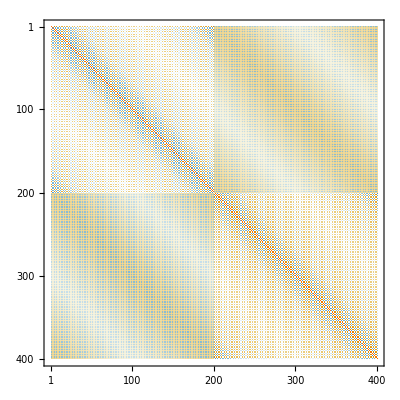

```mathematica
MatrixPlot[MTFDqpqp[{1.4,100,1,1/10,100}]]
```

```mathematica
(* Generate restricted CM in qpqp basis *)
MTFDres[var_,{dimA_,dimB_,d_}]:=Module[{Gfull,LengthL,ind},
Gfull=MTFDqpqp[var]; LengthL=Length[Gfull]/2;
ind=Join[Table[i,{i,2dimA}],Table[2(dimA+d)+i,{i,2dimB}],Table[LengthL+i,{i,2dimA}],Table[LengthL+2dimA+2d+i,{i,2dimB}]];
Gfull[[ind,ind]]];
```

```mathematica
MTFDres[var,subvar]//MatrixForm
```

(1.76728 | 0. | 0. | 0.
0. | 1.2766 | 0. | 0.
0. | 0. | 1.76728 | 0.
0. | 0. | 0. | 1.2766)

### Example for TFD State

```mathematica
t=1.4; (*Time*)
NN=10; (* number of lattice sites *)
δ=1.; (* lattice spacing *)
m=1/10; (* mass *)
β=100;  (*Inverse temperature*)
```

```mathematica
var={t,NN,δ,m,β};
```

```mathematica
dimA1=2; (* sites in subsystem A1 *)
dimB1=3; (* sites in subsystem B1 *)
dimPur=2(dimA1+dimB1); (* dimensions of the purifying system assuming minimal purification. We need the factor of 2 for the TFD because we have two copies of the system*)
dimA2=dimA1;
dimB2=dimB1;
d=1; (* distance between subsystem A1 and B1 *)
```

```mathematica
subvar={dimA1,dimB1,d};
```

```mathematica
MTFDqpqp[var]//MatrixForm
```

(1.76728 | 0. | 1.13782 | 0. | 0.944148 | 0. | 0.84646 | 0. | 0.797055 | 0. | 0.781758 | 0. | 0.797055 | 0. | 0.84646 | 0. | 0.944148 | 0. | 1.13782 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 1.2766 | 0. | -0.424417 | 0. | -0.0865386 | 0. | -0.0398191 | 0. | -0.0261367 | 0. | -0.0227773 | 0. | -0.0261367 | 0. | -0.0398191 | 0. | -0.0865386 | 0. | -0.424417 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
1.13782 | 0. | 1.76728 | 0. | 1.13782 | 0. | 0.944148 | 0. | 0.84646 | 0. | 0.797055 | 0. | 0.781758 | 0. | 0.797055 | 0. | 0.84646 | 0. | 0.944148 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | -0.424417 | 0. | 1.2766 | 0. | -0.424417 | 0. | -0.0865386 | 0. | -0.0398191 | 0. | -0.0261367 | 0. | -0.0227773 | 0. | -0.0261367 | 0. | -0.0398191 | 0. | -0.0865386 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.944148 | 0. | 1.13782 | 0. | 1.76728 | 0. | 1.13782 | 0. | 0.944148 | 0. | 0.84646 | 0. | 0.797055 | 0. | 0.781758 | 0. | 0.797055 | 0. | 0.84646 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | -0.0865386 | 0. | -0.424417 | 0. | 1.2766 | 0. | -0.424417 | 0. | -0.0865386 | 0. | -0.0398191 | 0. | -0.0261367 | 0. | -0.0227773 | 0. | -0.0261367 | 0. | -0.0398191 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.84646 | 0. | 0.944148 | 0. | 1.13782 | 0. | 1.76728 | 0. | 1.13782 | 0. | 0.944148 | 0. | 0.84646 | 0. | 0.797055 | 0. | 0.781758 | 0. | 0.797055 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | -0.0398191 | 0. | -0.0865386 | 0. | -0.424417 | 0. | 1.2766 | 0. | -0.424417 | 0. | -0.0865386 | 0. | -0.0398191 | 0. | -0.0261367 | 0. | -0.0227773 | 0. | -0.0261367 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.797055 | 0. | 0.84646 | 0. | 0.944148 | 0. | 1.13782 | 0. | 1.76728 | 0. | 1.13782 | 0. | 0.944148 | 0. | 0.84646 | 0. | 0.797055 | 0. | 0.781758 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | -0.0261367 | 0. | -0.0398191 | 0. | -0.0865386 | 0. | -0.424417 | 0. | 1.2766 | 0. | -0.424417 | 0. | -0.0865386 | 0. | -0.0398191 | 0. | -0.0261367 | 0. | -0.0227773 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.781758 | 0. | 0.797055 | 0. | 0.84646 | 0. | 0.944148 | 0. | 1.13782 | 0. | 1.76728 | 0. | 1.13782 | 0. | 0.944148 | 0. | 0.84646 | 0. | 0.797055 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | -0.0227773 | 0. | -0.0261367 | 0. | -0.0398191 | 0. | -0.0865386 | 0. | -0.424417 | 0. | 1.2766 | 0. | -0.424417 | 0. | -0.0865386 | 0. | -0.0398191 | 0. | -0.0261367 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.797055 | 0. | 0.781758 | 0. | 0.797055 | 0. | 0.84646 | 0. | 0.944148 | 0. | 1.13782 | 0. | 1.76728 | 0. | 1.13782 | 0. | 0.944148 | 0. | 0.84646 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | -0.0261367 | 0. | -0.0227773 | 0. | -0.0261367 | 0. | -0.0398191 | 0. | -0.0865386 | 0. | -0.424417 | 0. | 1.2766 | 0. | -0.424417 | 0. | -0.0865386 | 0. | -0.0398191 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.84646 | 0. | 0.797055 | 0. | 0.781758 | 0. | 0.797055 | 0. | 0.84646 | 0. | 0.944148 | 0. | 1.13782 | 0. | 1.76728 | 0. | 1.13782 | 0. | 0.944148 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | -0.0398191 | 0. | -0.0261367 | 0. | -0.0227773 | 0. | -0.0261367 | 0. | -0.0398191 | 0. | -0.0865386 | 0. | -0.424417 | 0. | 1.2766 | 0. | -0.424417 | 0. | -0.0865386 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.944148 | 0. | 0.84646 | 0. | 0.797055 | 0. | 0.781758 | 0. | 0.797055 | 0. | 0.84646 | 0. | 0.944148 | 0. | 1.13782 | 0. | 1.76728 | 0. | 1.13782 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | -0.0865386 | 0. | -0.0398191 | 0. | -0.0261367 | 0. | -0.0227773 | 0. | -0.0261367 | 0. | -0.0398191 | 0. | -0.0865386 | 0. | -0.424417 | 0. | 1.2766 | 0. | -0.424417 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
1.13782 | 0. | 0.944148 | 0. | 0.84646 | 0. | 0.797055 | 0. | 0.781758 | 0. | 0.797055 | 0. | 0.84646 | 0. | 0.944148 | 0. | 1.13782 | 0. | 1.76728 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | -0.424417 | 0. | -0.0865386 | 0. | -0.0398191 | 0. | -0.0261367 | 0. | -0.0227773 | 0. | -0.0261367 | 0. | -0.0398191 | 0. | -0.0865386 | 0. | -0.424417 | 0. | 1.2766 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1.76728 | 0. | 1.13782 | 0. | 0.944148 | 0. | 0.84646 | 0. | 0.797055 | 0. | 0.781758 | 0. | 0.797055 | 0. | 0.84646 | 0. | 0.944148 | 0. | 1.13782 | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1.2766 | 0. | -0.424417 | 0. | -0.0865386 | 0. | -0.0398191 | 0. | -0.0261367 | 0. | -0.0227773 | 0. | -0.0261367 | 0. | -0.0398191 | 0. | -0.0865386 | 0. | -0.424417
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1.13782 | 0. | 1.76728 | 0. | 1.13782 | 0. | 0.944148 | 0. | 0.84646 | 0. | 0.797055 | 0. | 0.781758 | 0. | 0.797055 | 0. | 0.84646 | 0. | 0.944148 | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.424417 | 0. | 1.2766 | 0. | -0.424417 | 0. | -0.0865386 | 0. | -0.0398191 | 0. | -0.0261367 | 0. | -0.0227773 | 0. | -0.0261367 | 0. | -0.0398191 | 0. | -0.0865386
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.944148 | 0. | 1.13782 | 0. | 1.76728 | 0. | 1.13782 | 0. | 0.944148 | 0. | 0.84646 | 0. | 0.797055 | 0. | 0.781758 | 0. | 0.797055 | 0. | 0.84646 | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.0865386 | 0. | -0.424417 | 0. | 1.2766 | 0. | -0.424417 | 0. | -0.0865386 | 0. | -0.0398191 | 0. | -0.0261367 | 0. | -0.0227773 | 0. | -0.0261367 | 0. | -0.0398191
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.84646 | 0. | 0.944148 | 0. | 1.13782 | 0. | 1.76728 | 0. | 1.13782 | 0. | 0.944148 | 0. | 0.84646 | 0. | 0.797055 | 0. | 0.781758 | 0. | 0.797055 | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.0398191 | 0. | -0.0865386 | 0. | -0.424417 | 0. | 1.2766 | 0. | -0.424417 | 0. | -0.0865386 | 0. | -0.0398191 | 0. | -0.0261367 | 0. | -0.0227773 | 0. | -0.0261367
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.797055 | 0. | 0.84646 | 0. | 0.944148 | 0. | 1.13782 | 0. | 1.76728 | 0. | 1.13782 | 0. | 0.944148 | 0. | 0.84646 | 0. | 0.797055 | 0. | 0.781758 | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.0261367 | 0. | -0.0398191 | 0. | -0.0865386 | 0. | -0.424417 | 0. | 1.2766 | 0. | -0.424417 | 0. | -0.0865386 | 0. | -0.0398191 | 0. | -0.0261367 | 0. | -0.0227773
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.781758 | 0. | 0.797055 | 0. | 0.84646 | 0. | 0.944148 | 0. | 1.13782 | 0. | 1.76728 | 0. | 1.13782 | 0. | 0.944148 | 0. | 0.84646 | 0. | 0.797055 | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.0227773 | 0. | -0.0261367 | 0. | -0.0398191 | 0. | -0.0865386 | 0. | -0.424417 | 0. | 1.2766 | 0. | -0.424417 | 0. | -0.0865386 | 0. | -0.0398191 | 0. | -0.0261367
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.797055 | 0. | 0.781758 | 0. | 0.797055 | 0. | 0.84646 | 0. | 0.944148 | 0. | 1.13782 | 0. | 1.76728 | 0. | 1.13782 | 0. | 0.944148 | 0. | 0.84646 | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.0261367 | 0. | -0.0227773 | 0. | -0.0261367 | 0. | -0.0398191 | 0. | -0.0865386 | 0. | -0.424417 | 0. | 1.2766 | 0. | -0.424417 | 0. | -0.0865386 | 0. | -0.0398191
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.84646 | 0. | 0.797055 | 0. | 0.781758 | 0. | 0.797055 | 0. | 0.84646 | 0. | 0.944148 | 0. | 1.13782 | 0. | 1.76728 | 0. | 1.13782 | 0. | 0.944148 | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.0398191 | 0. | -0.0261367 | 0. | -0.0227773 | 0. | -0.0261367 | 0. | -0.0398191 | 0. | -0.0865386 | 0. | -0.424417 | 0. | 1.2766 | 0. | -0.424417 | 0. | -0.0865386
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.944148 | 0. | 0.84646 | 0. | 0.797055 | 0. | 0.781758 | 0. | 0.797055 | 0. | 0.84646 | 0. | 0.944148 | 0. | 1.13782 | 0. | 1.76728 | 0. | 1.13782 | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.0865386 | 0. | -0.0398191 | 0. | -0.0261367 | 0. | -0.0227773 | 0. | -0.0261367 | 0. | -0.0398191 | 0. | -0.0865386 | 0. | -0.424417 | 0. | 1.2766 | 0. | -0.424417
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1.13782 | 0. | 0.944148 | 0. | 0.84646 | 0. | 0.797055 | 0. | 0.781758 | 0. | 0.797055 | 0. | 0.84646 | 0. | 0.944148 | 0. | 1.13782 | 0. | 1.76728 | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.424417 | 0. | -0.0865386 | 0. | -0.0398191 | 0. | -0.0261367 | 0. | -0.0227773 | 0. | -0.0261367 | 0. | -0.0398191 | 0. | -0.0865386 | 0. | -0.424417 | 0. | 1.2766)

```mathematica
MTFDres[var,subvar]//MatrixForm
```

(1.76728 | 0. | 1.13782 | 0. | 0.84646 | 0. | 0.797055 | 0. | 0.781758 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 1.2766 | 0. | -0.424417 | 0. | -0.0398191 | 0. | -0.0261367 | 0. | -0.0227773 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
1.13782 | 0. | 1.76728 | 0. | 0.944148 | 0. | 0.84646 | 0. | 0.797055 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | -0.424417 | 0. | 1.2766 | 0. | -0.0865386 | 0. | -0.0398191 | 0. | -0.0261367 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.84646 | 0. | 0.944148 | 0. | 1.76728 | 0. | 1.13782 | 0. | 0.944148 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | -0.0398191 | 0. | -0.0865386 | 0. | 1.2766 | 0. | -0.424417 | 0. | -0.0865386 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.797055 | 0. | 0.84646 | 0. | 1.13782 | 0. | 1.76728 | 0. | 1.13782 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | -0.0261367 | 0. | -0.0398191 | 0. | -0.424417 | 0. | 1.2766 | 0. | -0.424417 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.781758 | 0. | 0.797055 | 0. | 0.944148 | 0. | 1.13782 | 0. | 1.76728 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | -0.0227773 | 0. | -0.0261367 | 0. | -0.0865386 | 0. | -0.424417 | 0. | 1.2766 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1.76728 | 0. | 1.13782 | 0. | 0.84646 | 0. | 0.797055 | 0. | 0.781758 | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1.2766 | 0. | -0.424417 | 0. | -0.0398191 | 0. | -0.0261367 | 0. | -0.0227773
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1.13782 | 0. | 1.76728 | 0. | 0.944148 | 0. | 0.84646 | 0. | 0.797055 | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.424417 | 0. | 1.2766 | 0. | -0.0865386 | 0. | -0.0398191 | 0. | -0.0261367
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.84646 | 0. | 0.944148 | 0. | 1.76728 | 0. | 1.13782 | 0. | 0.944148 | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.0398191 | 0. | -0.0865386 | 0. | 1.2766 | 0. | -0.424417 | 0. | -0.0865386
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.797055 | 0. | 0.84646 | 0. | 1.13782 | 0. | 1.76728 | 0. | 1.13782 | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.0261367 | 0. | -0.0398191 | 0. | -0.424417 | 0. | 1.2766 | 0. | -0.424417
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.781758 | 0. | 0.797055 | 0. | 0.944148 | 0. | 1.13782 | 0. | 1.76728 | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.0227773 | 0. | -0.0261367 | 0. | -0.0865386 | 0. | -0.424417 | 0. | 1.2766)

#### Comparison with Bennet’s Code (?)

```mathematica
GTFDqpqp[{t,NN,δ,m,β}]//MatrixForm
```

(1.76728 | 0. | 1.13782 | 0. | 0.944148 | 0. | 0.84646 | 0. | 0.797055 | 0. | 0.781758 | 0. | 0.797055 | 0. | 0.84646 | 0. | 0.944148 | 0. | 1.13782 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 1.2766 | 0. | -0.424417 | 0. | -0.0865386 | 0. | -0.0398191 | 0. | -0.0261367 | 0. | -0.0227773 | 0. | -0.0261367 | 0. | -0.0398191 | 0. | -0.0865386 | 0. | -0.424417 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
1.13782 | 0. | 1.76728 | 0. | 1.13782 | 0. | 0.944148 | 0. | 0.84646 | 0. | 0.797055 | 0. | 0.781758 | 0. | 0.797055 | 0. | 0.84646 | 0. | 0.944148 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | -0.424417 | 0. | 1.2766 | 0. | -0.424417 | 0. | -0.0865386 | 0. | -0.0398191 | 0. | -0.0261367 | 0. | -0.0227773 | 0. | -0.0261367 | 0. | -0.0398191 | 0. | -0.0865386 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.944148 | 0. | 1.13782 | 0. | 1.76728 | 0. | 1.13782 | 0. | 0.944148 | 0. | 0.84646 | 0. | 0.797055 | 0. | 0.781758 | 0. | 0.797055 | 0. | 0.84646 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | -0.0865386 | 0. | -0.424417 | 0. | 1.2766 | 0. | -0.424417 | 0. | -0.0865386 | 0. | -0.0398191 | 0. | -0.0261367 | 0. | -0.0227773 | 0. | -0.0261367 | 0. | -0.0398191 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.84646 | 0. | 0.944148 | 0. | 1.13782 | 0. | 1.76728 | 0. | 1.13782 | 0. | 0.944148 | 0. | 0.84646 | 0. | 0.797055 | 0. | 0.781758 | 0. | 0.797055 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | -0.0398191 | 0. | -0.0865386 | 0. | -0.424417 | 0. | 1.2766 | 0. | -0.424417 | 0. | -0.0865386 | 0. | -0.0398191 | 0. | -0.0261367 | 0. | -0.0227773 | 0. | -0.0261367 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.797055 | 0. | 0.84646 | 0. | 0.944148 | 0. | 1.13782 | 0. | 1.76728 | 0. | 1.13782 | 0. | 0.944148 | 0. | 0.84646 | 0. | 0.797055 | 0. | 0.781758 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | -0.0261367 | 0. | -0.0398191 | 0. | -0.0865386 | 0. | -0.424417 | 0. | 1.2766 | 0. | -0.424417 | 0. | -0.0865386 | 0. | -0.0398191 | 0. | -0.0261367 | 0. | -0.0227773 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.781758 | 0. | 0.797055 | 0. | 0.84646 | 0. | 0.944148 | 0. | 1.13782 | 0. | 1.76728 | 0. | 1.13782 | 0. | 0.944148 | 0. | 0.84646 | 0. | 0.797055 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | -0.0227773 | 0. | -0.0261367 | 0. | -0.0398191 | 0. | -0.0865386 | 0. | -0.424417 | 0. | 1.2766 | 0. | -0.424417 | 0. | -0.0865386 | 0. | -0.0398191 | 0. | -0.0261367 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.797055 | 0. | 0.781758 | 0. | 0.797055 | 0. | 0.84646 | 0. | 0.944148 | 0. | 1.13782 | 0. | 1.76728 | 0. | 1.13782 | 0. | 0.944148 | 0. | 0.84646 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | -0.0261367 | 0. | -0.0227773 | 0. | -0.0261367 | 0. | -0.0398191 | 0. | -0.0865386 | 0. | -0.424417 | 0. | 1.2766 | 0. | -0.424417 | 0. | -0.0865386 | 0. | -0.0398191 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.84646 | 0. | 0.797055 | 0. | 0.781758 | 0. | 0.797055 | 0. | 0.84646 | 0. | 0.944148 | 0. | 1.13782 | 0. | 1.76728 | 0. | 1.13782 | 0. | 0.944148 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | -0.0398191 | 0. | -0.0261367 | 0. | -0.0227773 | 0. | -0.0261367 | 0. | -0.0398191 | 0. | -0.0865386 | 0. | -0.424417 | 0. | 1.2766 | 0. | -0.424417 | 0. | -0.0865386 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.944148 | 0. | 0.84646 | 0. | 0.797055 | 0. | 0.781758 | 0. | 0.797055 | 0. | 0.84646 | 0. | 0.944148 | 0. | 1.13782 | 0. | 1.76728 | 0. | 1.13782 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | -0.0865386 | 0. | -0.0398191 | 0. | -0.0261367 | 0. | -0.0227773 | 0. | -0.0261367 | 0. | -0.0398191 | 0. | -0.0865386 | 0. | -0.424417 | 0. | 1.2766 | 0. | -0.424417 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
1.13782 | 0. | 0.944148 | 0. | 0.84646 | 0. | 0.797055 | 0. | 0.781758 | 0. | 0.797055 | 0. | 0.84646 | 0. | 0.944148 | 0. | 1.13782 | 0. | 1.76728 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | -0.424417 | 0. | -0.0865386 | 0. | -0.0398191 | 0. | -0.0261367 | 0. | -0.0227773 | 0. | -0.0261367 | 0. | -0.0398191 | 0. | -0.0865386 | 0. | -0.424417 | 0. | 1.2766 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1.76728 | 0. | 1.13782 | 0. | 0.944148 | 0. | 0.84646 | 0. | 0.797055 | 0. | 0.781758 | 0. | 0.797055 | 0. | 0.84646 | 0. | 0.944148 | 0. | 1.13782 | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1.2766 | 0. | -0.424417 | 0. | -0.0865386 | 0. | -0.0398191 | 0. | -0.0261367 | 0. | -0.0227773 | 0. | -0.0261367 | 0. | -0.0398191 | 0. | -0.0865386 | 0. | -0.424417
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1.13782 | 0. | 1.76728 | 0. | 1.13782 | 0. | 0.944148 | 0. | 0.84646 | 0. | 0.797055 | 0. | 0.781758 | 0. | 0.797055 | 0. | 0.84646 | 0. | 0.944148 | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.424417 | 0. | 1.2766 | 0. | -0.424417 | 0. | -0.0865386 | 0. | -0.0398191 | 0. | -0.0261367 | 0. | -0.0227773 | 0. | -0.0261367 | 0. | -0.0398191 | 0. | -0.0865386
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.944148 | 0. | 1.13782 | 0. | 1.76728 | 0. | 1.13782 | 0. | 0.944148 | 0. | 0.84646 | 0. | 0.797055 | 0. | 0.781758 | 0. | 0.797055 | 0. | 0.84646 | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.0865386 | 0. | -0.424417 | 0. | 1.2766 | 0. | -0.424417 | 0. | -0.0865386 | 0. | -0.0398191 | 0. | -0.0261367 | 0. | -0.0227773 | 0. | -0.0261367 | 0. | -0.0398191
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.84646 | 0. | 0.944148 | 0. | 1.13782 | 0. | 1.76728 | 0. | 1.13782 | 0. | 0.944148 | 0. | 0.84646 | 0. | 0.797055 | 0. | 0.781758 | 0. | 0.797055 | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.0398191 | 0. | -0.0865386 | 0. | -0.424417 | 0. | 1.2766 | 0. | -0.424417 | 0. | -0.0865386 | 0. | -0.0398191 | 0. | -0.0261367 | 0. | -0.0227773 | 0. | -0.0261367
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.797055 | 0. | 0.84646 | 0. | 0.944148 | 0. | 1.13782 | 0. | 1.76728 | 0. | 1.13782 | 0. | 0.944148 | 0. | 0.84646 | 0. | 0.797055 | 0. | 0.781758 | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.0261367 | 0. | -0.0398191 | 0. | -0.0865386 | 0. | -0.424417 | 0. | 1.2766 | 0. | -0.424417 | 0. | -0.0865386 | 0. | -0.0398191 | 0. | -0.0261367 | 0. | -0.0227773
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.781758 | 0. | 0.797055 | 0. | 0.84646 | 0. | 0.944148 | 0. | 1.13782 | 0. | 1.76728 | 0. | 1.13782 | 0. | 0.944148 | 0. | 0.84646 | 0. | 0.797055 | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.0227773 | 0. | -0.0261367 | 0. | -0.0398191 | 0. | -0.0865386 | 0. | -0.424417 | 0. | 1.2766 | 0. | -0.424417 | 0. | -0.0865386 | 0. | -0.0398191 | 0. | -0.0261367
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.797055 | 0. | 0.781758 | 0. | 0.797055 | 0. | 0.84646 | 0. | 0.944148 | 0. | 1.13782 | 0. | 1.76728 | 0. | 1.13782 | 0. | 0.944148 | 0. | 0.84646 | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.0261367 | 0. | -0.0227773 | 0. | -0.0261367 | 0. | -0.0398191 | 0. | -0.0865386 | 0. | -0.424417 | 0. | 1.2766 | 0. | -0.424417 | 0. | -0.0865386 | 0. | -0.0398191
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.84646 | 0. | 0.797055 | 0. | 0.781758 | 0. | 0.797055 | 0. | 0.84646 | 0. | 0.944148 | 0. | 1.13782 | 0. | 1.76728 | 0. | 1.13782 | 0. | 0.944148 | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.0398191 | 0. | -0.0261367 | 0. | -0.0227773 | 0. | -0.0261367 | 0. | -0.0398191 | 0. | -0.0865386 | 0. | -0.424417 | 0. | 1.2766 | 0. | -0.424417 | 0. | -0.0865386
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.944148 | 0. | 0.84646 | 0. | 0.797055 | 0. | 0.781758 | 0. | 0.797055 | 0. | 0.84646 | 0. | 0.944148 | 0. | 1.13782 | 0. | 1.76728 | 0. | 1.13782 | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.0865386 | 0. | -0.0398191 | 0. | -0.0261367 | 0. | -0.0227773 | 0. | -0.0261367 | 0. | -0.0398191 | 0. | -0.0865386 | 0. | -0.424417 | 0. | 1.2766 | 0. | -0.424417
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1.13782 | 0. | 0.944148 | 0. | 0.84646 | 0. | 0.797055 | 0. | 0.781758 | 0. | 0.797055 | 0. | 0.84646 | 0. | 0.944148 | 0. | 1.13782 | 0. | 1.76728 | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.424417 | 0. | -0.0865386 | 0. | -0.0398191 | 0. | -0.0261367 | 0. | -0.0227773 | 0. | -0.0261367 | 0. | -0.0398191 | 0. | -0.0865386 | 0. | -0.424417 | 0. | 1.2766)

```mathematica
(GTFDqpqp[{t,NN,δ,m,β}]-MTFDqpqp[var])//Chop//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
GTFDres[var,{dimA1,dimB1,d}]//MatrixForm
```

(1.76728 | 0. | 1.13782 | 0. | 0.84646 | 0. | 0.797055 | 0. | 0.781758 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 1.2766 | 0. | -0.424417 | 0. | -0.0398191 | 0. | -0.0261367 | 0. | -0.0227773 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
1.13782 | 0. | 1.76728 | 0. | 0.944148 | 0. | 0.84646 | 0. | 0.797055 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | -0.424417 | 0. | 1.2766 | 0. | -0.0865386 | 0. | -0.0398191 | 0. | -0.0261367 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.84646 | 0. | 0.944148 | 0. | 1.76728 | 0. | 1.13782 | 0. | 0.944148 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | -0.0398191 | 0. | -0.0865386 | 0. | 1.2766 | 0. | -0.424417 | 0. | -0.0865386 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.797055 | 0. | 0.84646 | 0. | 1.13782 | 0. | 1.76728 | 0. | 1.13782 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | -0.0261367 | 0. | -0.0398191 | 0. | -0.424417 | 0. | 1.2766 | 0. | -0.424417 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.781758 | 0. | 0.797055 | 0. | 0.944148 | 0. | 1.13782 | 0. | 1.76728 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | -0.0227773 | 0. | -0.0261367 | 0. | -0.0865386 | 0. | -0.424417 | 0. | 1.2766 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1.76728 | 0. | 1.13782 | 0. | 0.84646 | 0. | 0.797055 | 0. | 0.781758 | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1.2766 | 0. | -0.424417 | 0. | -0.0398191 | 0. | -0.0261367 | 0. | -0.0227773
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1.13782 | 0. | 1.76728 | 0. | 0.944148 | 0. | 0.84646 | 0. | 0.797055 | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.424417 | 0. | 1.2766 | 0. | -0.0865386 | 0. | -0.0398191 | 0. | -0.0261367
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.84646 | 0. | 0.944148 | 0. | 1.76728 | 0. | 1.13782 | 0. | 0.944148 | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.0398191 | 0. | -0.0865386 | 0. | 1.2766 | 0. | -0.424417 | 0. | -0.0865386
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.797055 | 0. | 0.84646 | 0. | 1.13782 | 0. | 1.76728 | 0. | 1.13782 | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.0261367 | 0. | -0.0398191 | 0. | -0.424417 | 0. | 1.2766 | 0. | -0.424417
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.781758 | 0. | 0.797055 | 0. | 0.944148 | 0. | 1.13782 | 0. | 1.76728 | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.0227773 | 0. | -0.0261367 | 0. | -0.0865386 | 0. | -0.424417 | 0. | 1.2766)

```mathematica
TFDRestrictionAA[{dimA1,dimB1,dimA2,dimB2}]
```

{1,2,3,4,11,12,13,14,21,22,23,24,31,32,33,34}

Works!

## 1. Complexity of Purification

### Pre-algorithm: Create complex structures and initial transformations

```mathematica
CM0=MTFDres[var,subvar];
{rlist,MTra}=GOExtractStdFormG[CM0]//Re;
JT=GOPurifyStandardJBoson[rlist,dimPur,"qpqp"];
JR=GOTransformGtoJ[IdentityMatrix[2(2dimA1+2dimB1+dimPur)],"qpqp","qpqp"]; (* Note again the factor of 2 *)

J0=JR;
M0=ArrayFlatten[{{MTra,0},{0,IdentityMatrix[2dimPur]}}]//SparseArray; (* Attention: For complexity, we need to put MTra, because JR transforms inversely to JT!!! *)
```

### 1. Define the problem-specific input arguments

```mathematica
function=GOCoPBos[JT]; gradient=GOCoPgradBos[JT];
ProblemSpecific={function,gradient};
```

### 2. Define the system-specific input arguments

```mathematica
LieBasis=GOLieBasisCompound[{GOLieBasisEmpty[2(dimA1+dimB1)],GOLieBasisSpNoUN[dimPur]}]; (* Note again the factor of 2 *)
M0List=Table[MatrixExp[RandomReal[{0,0.7},Length[LieBasis]].LieBasis].M0,{i,10}];
geometry=GOGeometryConst[LieBasis,J0,+1];
newM[m_,s_,x_]:=m.GOapproxExp[s,x];
```

```mathematica
SystemSpecific={J0,M0List,LieBasis,geometry,newM};
```

### 3. Define the procedure-specific input arguments

```mathematica
stepcorrection[s_]:=s/2; (* How to correct the step size *)
gradienttolerance=10^-6; (* Tolerance for gradient *)
valuetolerance=10^-5; (* Tolerance of two successive function values *)
steplimit=∞; (* Stop after some finite number of steps, regardless of convergence*)
persueall=False; (* Here we specify that all 50 initial trajectories should be pursured until convergence *)
ProcedureSpecific={gradienttolerance,valuetolerance,steplimit,stepcorrection,persueall};
```

### Run the Optimization and evaluate results

```mathematica
{time,Result}=Timing[GOOptimize[ProblemSpecific,SystemSpecific,ProcedureSpecific]];
```

Reason for termination: Function value tolerance reached

Time taken: 59.7488 seconds

Final value: 1.69989

Number of iterations: 6

Number of total corrections: 0

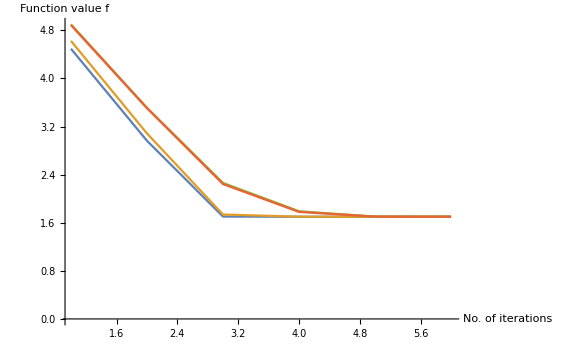

```mathematica
Print["Reason for termination: ",Result[[7]]];
Print["Time taken: ",time," seconds"];
Print["Final value: ",Result⟦1,1⟧];
Print["Number of iterations: ",Length[Result⟦4,1⟧]];
Print["Number of total corrections: ",Result⟦3⟧//Total];
ListPlot[Result⟦5⟧, ImageSize->Large, AxesLabel->{"No. of iterations","Function value f"},PlotRange->All,Joined->True]
```